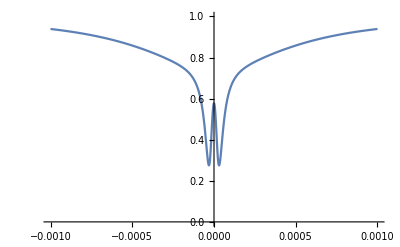

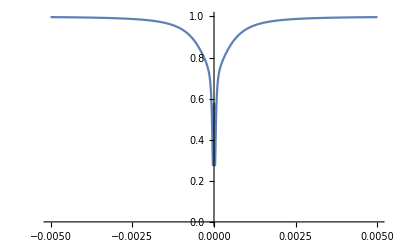

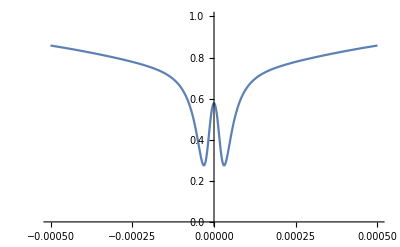

```mathematica
n:=1.44
λ:=1550 10^(-9)
R1:= 100 10^(-6)
R2:= 200 10^(-6)
R3:= 200 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=5× 10^7
Q2:= 1 × 10^8
Q3:= 5 × 10^8
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=15
x2:=0.00008
x3:=0.000058
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
δ2:=δ1
δ3:=δ1
δ1min:=-0.001;
δ1max:=0.001;
ref:=(r1 - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-r1 r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))
r1a:=(r2 -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-r2   r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(r3 -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-r3 ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[Abs[ref]^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
Plot[Abs[ref]^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[Abs[ref]^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
transdata:=Table[{δ1,Abs[ref]^2},{δ1,-0.1, 0.1, 0.000001}]
(*Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
 Plot[groupindex,{δ1,δ1min,δ1max}, PlotRange->All]*)
```

```mathematica
Export["3_EIA_EIT.csv",transdata]
```

3_EIA_EIT.csv

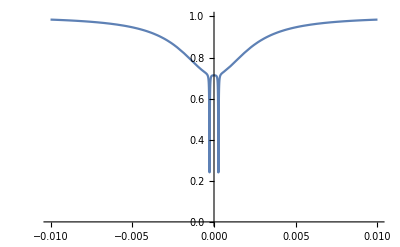

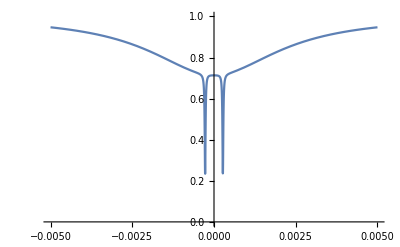

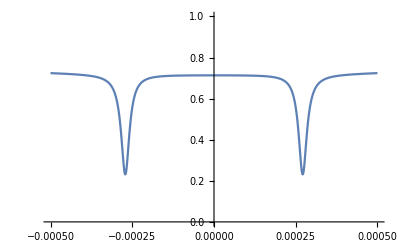

```mathematica
n:=1.44
λ:=1550 10(-9)
R1:= 100 10^(-6)
R2:= 200 10^(-6)
R3:= 200 10^(-6)
d1:= 2 Pi R1
d2:=2 Pi R2
d3:= 2 Pi R3
Q1:=1× 10^7
Q2:= 3 × 10^8
Q3:=3 × 10^8
α1:= (2 Pi n)/(Q1  λ)
α2:= (2 Pi n)/(Q2  λ)
α3:= (2 Pi n)/(Q3  λ)
x1:=12
x2:=0.0006
x3:=0.003
T1:= x1  α1  d1
T2:= x2  α2  d2
T3:= x3  α3  d3
r1:=√(1-T1)
r2:=√(1-T2)
r3:=√(1-T3)
a1:=ⅇ^(-(α1 d1)/2)
a2:=ⅇ^(-(α2  d2)/2)
a3:=ⅇ^(-(α3 d3)/2)
ϕ1:=δ1
ϕ2:=δ2
ϕ3:=δ3
δ2:=δ1+0.000000001
δ3:=δ1-0.000000001
δ1min:=-0.01;
δ1max:=0.01;
ref:=(r1 - r1a    ⅇ^(ⅈ δ1 -(α1 d1)/2))/(1-r1 r1a ⅇ^(ⅈ δ1 - (α1 d1)/2))
r1a:=(r2 -  r2a   ⅇ^(ⅈ  δ2 -(α2  d2)/2))/(1-r2   r2a ⅇ^(ⅈ   δ2 - (α2  d2)/2))
r2a:=(r3 -     ⅇ^(ⅈ  δ3 -(α3  d3)/2))/(1-r3 ⅇ^(ⅈ   δ3 - (α3  d3)/2))
Plot[Abs[ref]^2,{δ1,δ1min,δ1max}, PlotRange->{0,1}]
Plot[Abs[ref]^2,{δ1,-0.005,0.005}, PlotRange->{0,1}]
Plot[Abs[ref]^2,{δ1,-0.0005,0.0005}, PlotRange->{0,1}]
(*Plot[ϕ1eff,{δ1,δ1min,δ1max}, PlotRange->All, PlotPoints->200]
Plot[ϕ2eff,{δ1,δ1min,δ1max}, PlotRange->All]
Plot[ϕ3eff,{δ1,δ1min,δ1max}, PlotRange->All]
 Plot[groupindex,{δ1,δ1min,δ1max}, PlotRange->All]*)
```